```mathematica
Clear["Global*`"]
```

## Training

## Modeling Input/Aero Forces

We want to model the the force from each motor/rotor i, F_i.

(v^·)_B=1/m F_B-ω_B×v_B-Qᵀg
F_B=∑_(l ∈Motors) F_l
F_B=m((v^·)_B+ω_B×v_B+Qᵀg)

The first method we use to do this is the modeling each each

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ)ᵀ
(F̂)_B:ℝ^10→ℝ^3

Here Ω is the rotor velocity of each motor and v_B and ω_B are the body linear and rotational velocities.
Modeling this as a second order polynomial, we can write F_B using Einstein tensor notation as:

((F̂)_B)_i=A_i+∑_(j=1)^(#x) B_(i,j)x_j+∑_(j=1)^Abs[x] ∑_(k=1)^Abs[x] C_(i,j,k)x_j x_k

Here A is a column vector (bias term), B is a matrix (linear term), C is a 3rd order tensor (quadratic term). Inorder to use linear algebra tools we can reorder this into a matrix problem as follows:

D=(A_(3x 1) | B_(3×Abs[x]) | (C_(i,j,1) | … | C_(i,j,Abs[x]))_(3×(Abs[x]·Abs[x]))), z=(𝟙
x
x⊗x)
(F̂)_B=D z ⟹ (F̂)_B ᵀ=zᵀDᵀ 
D≡3×(1+Abs[x]+Abs[x]^2)

Where ⊗ denotes the Kronecker product and Abs[x]is the dimension of the vector x.

F_B=∑_(l ∈Motors) D_l x_l=D_1 x_1+D_2 x_2+D_3 x_3+D_4 x_4=(D_1 | D_2 | D_3 | D_4)(x_1
x_2
x_3
x_4)
D=(D_1 | D_2 | D_3 | D_4)

## Modeling Input/Aero Moments

Starting from Euler’s equation:

(ω^·)_B=J^-1(τ_B-ω_B×J ω_B)
τ_B=J(ω^·)_B+ω_B×J ω_B

Again modeling it as a quadratic of x. However this time it is important to use Ω̇, to capture conservation of angular momentum’s impact on body torque

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ | Ω̇ ᵀ)ᵀ
(τ̂)_B:ℝ^14→ℝ^3

We can again express this as a matrix problem as follows:

((τ̂)_B)_i=A_i+∑_(j=1)^(#x) B_(i,j)x_l_j+∑_(j=1)^Abs[x] ∑_(k=1)^Abs[x] C_(i,j,k)x_l_j x_l_k
D=(A_(3x 1) | B_(3×Abs[x]) | (C_(i,j,1) | … | C_(i,j,Abs[x]))_(3×(Abs[x]·Abs[x]))), z=(𝟙
x
x⊗x)
(τ̂)_B=D z ⟹ (τ̂)_B ᵀ=zᵀDᵀ 
D≡3×(1+Abs[x]+Abs[x]^2)

## Fitting Model

### Importing Data

Loading the segments comprising one full flight and concatenating

```mathematica
(*Loading Flight 1*)
trainData=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-12-22_seg_1.csv"];
header=trainData⟦1,;;⟧;
trainData11=trainData⟦2;;,;;⟧;
trainData12=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-12-22_seg_2.csv",HeaderLines->1];
trainData13=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-12-22_seg_3.csv",HeaderLines->1];
trainData14=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-12-22_seg_4.csv",HeaderLines->1];
trainData1=Join[trainData11,trainData12,trainData13,trainData14,1];
(*Loading Flight 2*)
trainData21=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-55-55_seg_1.csv",HeaderLines->1];
trainData22=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-55-55_seg_2.csv",HeaderLines->1];
trainData23=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-55-55_seg_3.csv",HeaderLines->1];
trainData2=Join[trainData21,trainData22,trainData23,1];
(*Loading Flight 3*)
trainData31=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-17-14-47_seg_1.csv",HeaderLines->1];
trainData32=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-17-14-47_seg_2.csv",HeaderLines->1];
trainData3=Join[trainData31,trainData32,1];
(*Concatenating all the data for easy use*)
trainData=Join[trainData1,trainData2,trainData3,1];
```

Plotting this data of quad rotors position through time

```mathematica
Module[{pos1,downSample1,pos2,downSample2,pos3,downSample3},
pos1=trainData1⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample1=Table[pos1⟦n⟧,{n,1,Length[pos1],20}];
pos2=trainData2⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample2=Table[pos2⟦n⟧,{n,1,Length[pos2],20}];
pos3=trainData3⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample3=Table[pos3⟦n⟧,{n,1,Length[pos3],20}];
{{
Show[
ListPointPlot3D[downSample1,PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{First[pos1]},PlotStyle->{Red,Large}],
ListPointPlot3D[{Last[pos1]},PlotStyle->{Green,Large}]
],
Show[
ListPointPlot3D[downSample2,PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{First[pos2]},PlotStyle->{Red,Large}],
ListPointPlot3D[{Last[pos2]},PlotStyle->{Green,Large}]
],
Show[
ListPointPlot3D[downSample3,PlotTheme->"Detailed",PlotRange->All,ImageSize->Medium]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{First[pos3]},PlotStyle->{Red,Large}],
ListPointPlot3D[{Last[pos3]},PlotStyle->{Green,Large}]
]
}}//TableForm
]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

The first flight is a aggressive linear oscillation, the second flight is a wobbly circle, and the third flight is a aggressive 3d circle. The flights cover different regimes of motion/actuation. The first trajectory in particular forces the quad through its own prop wash.

### Extracting Data

```mathematica
Squeeze[A_]:=ArrayReshape[A,Dimensions[A]~DeleteCases~1];
x=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
vDot=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;
Ω=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;
ΩDot=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"dmot 1","dmot 2","dmot 3","dmot 4"}⟧;v=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;ω=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
ωDot=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"ang acc x","ang acc y","ang acc z"}⟧;
q=trainData⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

### Force Model

#### Examining The Data

Plotting the body’s position and acceleration over the two flights.

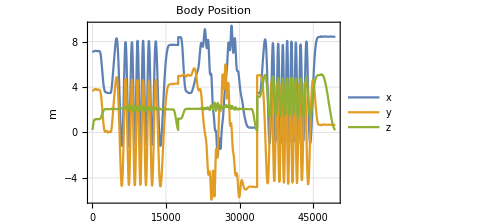
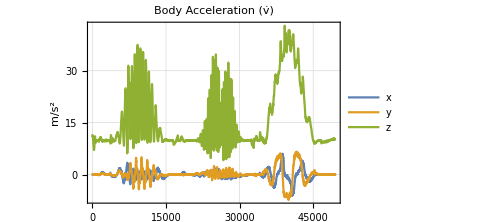
-Graphics- | -Graphics-

```mathematica
{{ListPlot[xᵀ,
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Body Position",
PlotLegends->{"x","y","z"},
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m"}],
ListPlot[vDotᵀ,
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Body Acceleration (v̇)",
PlotLegends->{"x","y","z"},
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]}}//TableForm
```

From this we see that when the quad rotors body is stationary the recorded acceleration of the body is ~10m/s^2. Thus we note that the data labeled “acceleration body x”, “acceleration body y”, “acceleration body z” is actually a filtered fusion Vicon/IMU measurement. Thus we can modify our force fitting function:

F_B=m((v^·)_imu+ω_B×v_B)

Removing Coriolis from acceleration each time step:

```mathematica
m=1.776;
𝕐𝒻=m(vDot+MapThread[#1×#2&,{ω,v}]);
```

Here ŷ is the net forces applied on the quad rotor by the quad rotor as well as the aerodynamic forces on the quad rotor.

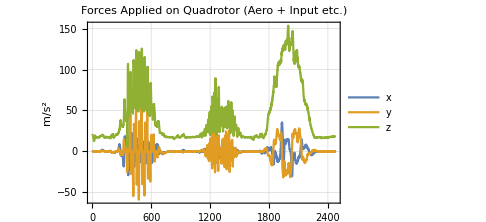

```mathematica
ListPlot[𝕐𝒻⟦;;;;20⟧ᵀ,
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Forces Applied on Quadrotor (Aero + Input etc.)",
PlotLegends->{"x","y","z"},
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
```

Here we plot the motor speeds

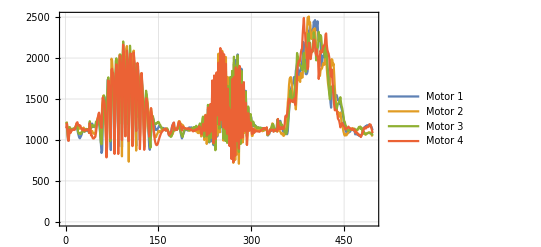

```mathematica
ListPlot[Ω⟦;;;;100⟧ᵀ,
PlotTheme->"Detailed",
Joined->True,
PlotRange->Full,
PlotLegends->{"Motor 1","Motor 2","Motor 3","Motor 4"}]
```

#### Fitting Force

As above we assume the forces on the quad rotor are a function of only the body linear and angular velocity, as well as the motor speeds.

x=(v_B ᵀ | ω_B ᵀ | Ω)ᵀ
F_B[x]:ℝ^10→ℝ^3

We are then going to be fitting 1/m

F_B=m((v^·)_imu+ω_B×v_B)

As  F_B is modeled as a quadratic we must apply the transform z=𝒻(x)=(𝟙
x
x⊗x). Constructing the set of sample points.

```mathematica
m=1.776;
ℤ𝒻=Module[{X,𝕏,𝒻},
𝕏=Join[v,ω,Ω,2];
X=Table[{Slot[i]},{i,Dimensions[𝕏]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
MapThread[𝒻,𝕏ᵀ]
];
```

Finally we can now compute the matrix 𝔻, 𝔼

```mathematica
𝕐𝒻=m(vDot+MapThread[#1×#2&,{ω,v}]);
𝔻=Module[{n=15},
(PseudoInverse[ℤ𝒻⟦;;;;n⟧].𝕐𝒻⟦;;;;n⟧)ᵀ
];
```

#### Measuring Goodness of Fit

We can then evaluate the performance of this model using

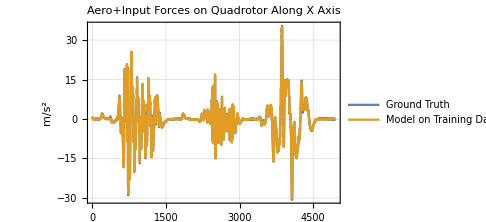
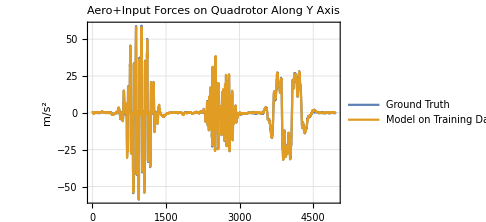
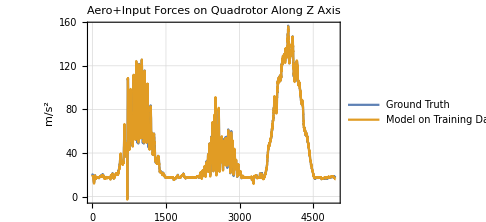
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruth,trainingOutput,labels},
groundTruth=𝕐𝒻⟦;;;;10⟧ᵀ;
trainingOutput=((𝔻.ℤ𝒻ᵀ)ᵀ⟦;;;;10⟧)ᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruth⟦i⟧,trainingOutput⟦i⟧},PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Training Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]}
]//TableForm
```

Checking the goodness of fit using the coefficient of determination:

ȳ=1/N∑_(i=1)^N y_i
R^2=1-(∑_i Norm[y_i-f(x_i)])/(∑_i Norm[y_i-ȳ])

We compute the R^2 coefficient then:

```mathematica
Module[{𝓎𝒻,𝕗,N},
𝓎𝒻=Mean[𝕐𝒻];𝕗=(𝔻.ℤ𝒻ᵀ)ᵀ;N=Length[𝕗];
1-(∑_(i=1)^N Norm[𝕐𝒻⟦i⟧-𝕗⟦i⟧])/(∑_(i=1)^N Norm[𝕐𝒻⟦i⟧-𝓎𝒻])
]
```

0.977039

#### Saving the quadratic least squares matrix:

```mathematica
Export[NotebookDirectory[]<>"/model_parameters/QuadraticLeastSquaresForces.mat",𝔻];
Module[{test},
test=Import[NotebookDirectory[]<>"/model_parameters/QuadraticLeastSquaresForces.mat"]⟦1⟧;
test==𝔻
]
```

True

### Torque Model

#### Fitting Torque

As above we assume the forces on the quad rotor are a function of only the body linear and angular velocity, as well as the motor speeds.

x=(v_B ᵀ | ω_B ᵀ | Ωᵀ | Ω̇ ᵀ)ᵀ
(τ̂)_B[x]:ℝ^14→ℝ^3

(τ̂)_B(x)=J(ω^·)_B+ω_B×J ω_B

As  F_B is modeled as a quadratic we must apply the transform z=𝒻(x)=(𝟙
x
x⊗x). Constructing the set of sample points.

```mathematica
J=({{0.01566089, 0.00000318037, 0.}, {0.00000318037, 0.01562078, 0.}, {0., 0., 0.02226868}});
ℤ𝓉=Module[{X,𝕏,𝒻},
𝕏=Join[v,ω,Ω,ΩDot,2];
X=Table[{Slot[i]},{i,Dimensions[𝕏]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
MapThread[𝒻,𝕏ᵀ]
];
```

Finally we can now compute the matrix 𝔻, 𝔼

```mathematica
𝕐𝓉=MapThread[J.#1+#2×(J.#2)&,{ωDot,ω}];
𝔼=Module[{n=10},
(PseudoInverse[ℤ𝓉⟦;;;;n⟧].𝕐𝓉⟦;;;;n⟧)ᵀ
];
```

#### Measuring Goodness of Fit

We can then evaluate the performance of this model using

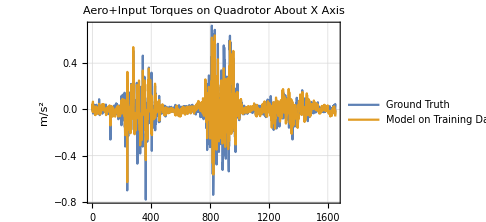
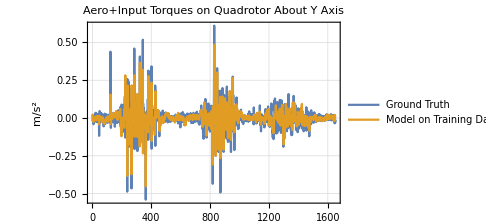
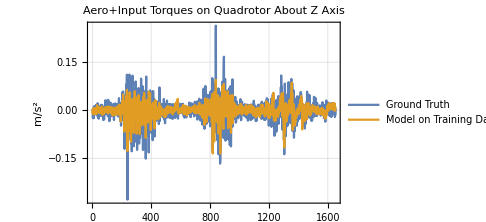
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruth,trainingOutput,labels},
groundTruth=𝕐𝓉⟦;;;;30⟧ᵀ;
trainingOutput=((𝔼.ℤᵀ)ᵀ⟦;;;;30⟧)ᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruth⟦i⟧,trainingOutput⟦i⟧},PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Torques on Quadrotor About "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Training Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]}
]//TableForm
```

Checking the goodness of fit using the coefficient of determination:

ȳ=1/N∑_(i=1)^N y_i
R^2=1-(∑_i Norm[y_i-f(x_i)])/(∑_i Norm[y_i-ȳ])

We compute the R^2 coefficient then:

```mathematica
Module[{𝓎,τ,N},
𝓎=Mean[𝕐𝓉];τ=(𝔼.ℤ𝓉ᵀ)ᵀ;N=Length[τ];
1-(∑_(i=1)^N Norm[𝕐𝓉⟦i⟧-τ⟦i⟧])/(∑_(i=1)^N Norm[𝕐𝓉⟦i⟧-𝓎])
]
```

0.284333

#### Saving the quadratic least squares matrix:

```mathematica
Export[NotebookDirectory[]<>"/model_parameters/QuadraticLeastSquaresTorques.mat",𝔼];
Module[{test},
test=Import[NotebookDirectory[]<>"/model_parameters/QuadraticLeastSquaresTorques.mat"]⟦1⟧;
test==𝔼
]
```

True

## Testing Dataset 1

### Importing Data

Loading in the testing data

```mathematica
testData1=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-54-06_seg_1.csv",HeaderLines->1];
testData2=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-54-06_seg_2.csv",HeaderLines->1];
testData3=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-54-06_seg_3.csv",HeaderLines->1];
testData4=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-13-54-06_seg_4.csv",HeaderLines->1];
testData=Join[testData1,testData2,testData3,testData4,1];
```

```mathematica
Module[{pos,downSample},
pos=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],20}];
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed",PlotRange->All]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{First[pos]},PlotStyle->{Red,Large}],
ListPointPlot3D[{Last[pos]},PlotStyle->{Green,Large}]
]
]
```

-Graphics3D-

### Extracting Data

```mathematica
Ω=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;
ΩDot=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"dmot 1","dmot 2","dmot 3","dmot 4"}⟧;v=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;vDot=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;ω=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
ωDot=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"ang acc x","ang acc y","ang acc z"}⟧;
q=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

### Testing Fitted Model

Redefining quadratic transformation and applying on data set

```mathematica
m=1.776;J=({{0.01566089, 0.00000318037, 0.}, {0.00000318037, 0.01562078, 0.}, {0., 0., 0.02226868}});

ℤ𝒻=Module[{X,𝕏,𝒻},
𝕏=Join[v,ω,Ω,2];
X=Table[{Slot[i]},{i,Dimensions[𝕏]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
MapThread[𝒻,𝕏ᵀ]];
ℤ𝓉=Module[{X,𝕏,𝒻},
𝕏=Join[v,ω,Ω,ΩDot,2];
X=Table[{Slot[i]},{i,Dimensions[𝕏]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
MapThread[𝒻,𝕏ᵀ]
];
```

Computing the ground truth

```mathematica
𝕐𝒻=m(vDot+MapThread[#1×#2&,{ω,v}]);
𝕐𝓉=MapThread[J.#1+#2×(J.#2)&,{ωDot,ω}];
```

### Test data Goodness of Fit

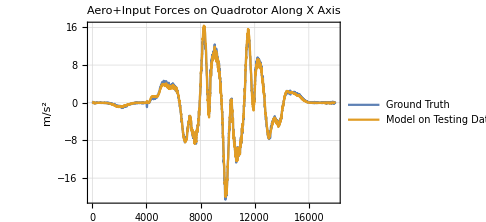
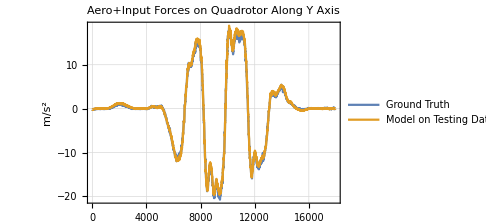
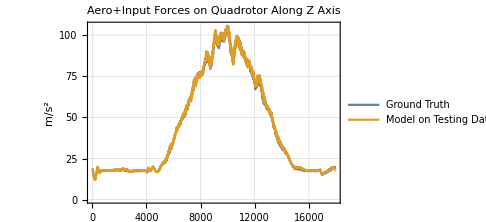
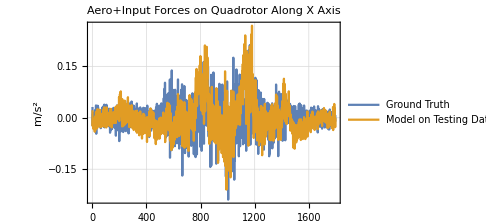
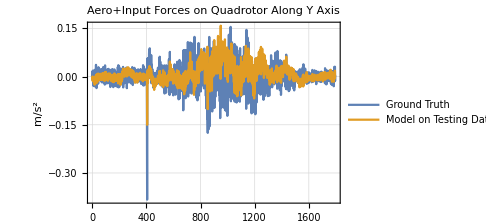
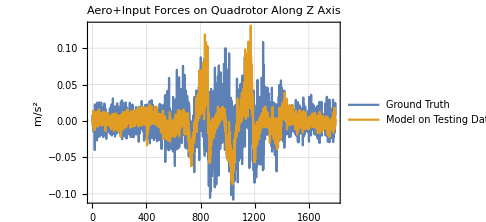
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruthF,testingOutputF,groundTruthT,testingOutputT,labels},
groundTruthF=𝕐𝒻ᵀ;
testingOutputF=𝔻.ℤ𝒻ᵀ;
groundTruthT=𝕐𝓉ᵀ;
testingOutputT=𝔼.ℤ𝓉ᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruthF⟦i⟧,testingOutputF⟦i⟧},
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Testing Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}],
Table[
ListPlot[{groundTruthT⟦i,;;;;10⟧,testingOutputT⟦i,;;;;10⟧},
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Testing Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]
}
]//TableForm
```

```mathematica
Module[{𝓎f,𝓎t,𝕗,τ,N},
𝓎f=Mean[𝕐𝒻];𝓎t=Mean[𝕐𝓉];𝕗=(𝔻.ℤ𝒻ᵀ)ᵀ;τ=(𝔼.ℤ𝓉ᵀ)ᵀ;N=Length[𝕗];
{1-(∑_(i=1)^N Norm[𝕐𝒻⟦i⟧-𝕗⟦i⟧])/(∑_(i=1)^N Norm[𝕐𝒻⟦i⟧-𝓎f]),
1-(∑_(i=1)^N Norm[𝕐𝓉⟦i⟧-τ⟦i⟧])/(∑_(i=1)^N Norm[𝕐𝓉⟦i⟧-𝓎t])}//TableForm
]
```

0.972797
-0.0775922

## Testing Dataset 2

### Importing Data

Loading in the testing data

```mathematica
testData1=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-10-37_seg_1.csv",HeaderLines->1];
testData2=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-10-37_seg_2.csv",HeaderLines->1];
testData3=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-10-37_seg_3.csv",HeaderLines->1];
testData4=Import[NotebookDirectory[]<>"processed_data/merged_2021-02-03-16-10-37_seg_4.csv",HeaderLines->1];
testData=Join[testData1,testData2,testData3,testData4,1];
```

```mathematica
Module[{pos,downSample},
pos=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"pos x","pos y","pos z"}⟧;
downSample=Table[pos⟦n⟧,{n,1,Length[pos],20}];
Show[
ListPointPlot3D[downSample,PlotTheme->"Detailed",PlotRange->All]/.Point[a___]:>{Thick,Line[a]},
ListPointPlot3D[{First[pos]},PlotStyle->{Red,Large}],
ListPointPlot3D[{Last[pos]},PlotStyle->{Green,Large}]
]
]
```

-Graphics3D-

### Extracting Data

```mathematica
Ω=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"mot 1","mot 2","mot 3","mot 4"}⟧;
ΩDot=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"dmot 1","dmot 2","dmot 3","dmot 4"}⟧;v=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"vel x","vel y","vel z"}⟧;vDot=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"acc x","acc y","acc z"}⟧;ω=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"ang vel x","ang vel y","ang vel z"}⟧;
ωDot=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"ang acc x","ang acc y","ang acc z"}⟧;
q=testData⟦;;,Position[header,#]⟦1,1⟧&/@{"quat w","quat x","quat y","quat z"}⟧;
```

Converting set of quaternions to a set of Rotation matrices

```mathematica
ℛ=2({{(#⟦1⟧)^2+(#⟦2⟧)^2-1/2, #⟦2⟧#⟦3⟧-#⟦1⟧#⟦4⟧, #⟦2⟧#⟦4⟧+#⟦1⟧#⟦3⟧}, {#⟦2⟧#⟦3⟧+#⟦1⟧#⟦4⟧, (#⟦1⟧)^2+(#⟦3⟧)^2-1/2, #⟦3⟧#⟦4⟧-#⟦1⟧#⟦2⟧}, {#⟦2⟧#⟦4⟧-#⟦1⟧#⟦3⟧, #⟦3⟧#⟦4⟧+#⟦1⟧#⟦2⟧, (#⟦1⟧)^2+(#⟦4⟧)^2-1/2}})&/@q;
```

### Testing Fitted Model

Redefining quadratic transformation and applying on data set

```mathematica
m=1.776;J=({{0.01566089, 0.00000318037, 0.}, {0.00000318037, 0.01562078, 0.}, {0., 0., 0.02226868}});

(*Transformed dataset for Force model*)
ℤ𝒻=Module[{X,𝕏,𝒻},
𝕏=Join[v,ω,Ω,2];
X=Table[{Slot[i]},{i,Dimensions[𝕏]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
MapThread[𝒻,𝕏ᵀ]
];
(*Transformed dataset for Torque model*)
ℤ𝓉=Module[{X,𝕏,𝒻},
𝕏=Join[v,ω,Ω,ΩDot,2];
X=Table[{Slot[i]},{i,Dimensions[𝕏]⟦2⟧}];
𝒻=Evaluate[Squeeze[Join[{{1}},X,KroneckerProduct[X,X]]]]&;
MapThread[𝒻,𝕏ᵀ]
];
```

Computing the ground truth

```mathematica
𝕐𝒻=m(vDot+MapThread[#1×#2&,{ω,v}]);
𝕐𝓉=MapThread[J.#1+#2×(J.#2)&,{ωDot,ω}];
```

### Test data Goodness of Fit

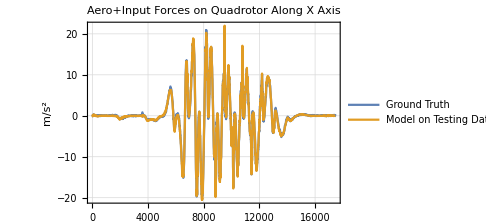
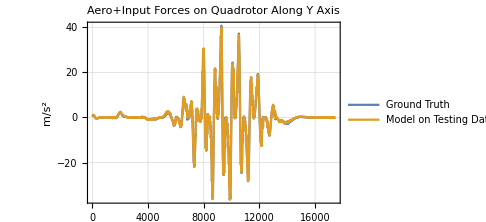
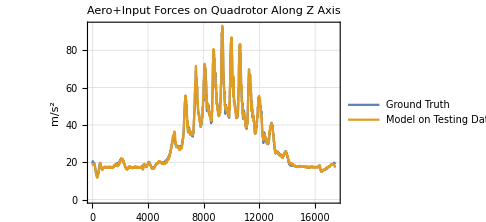
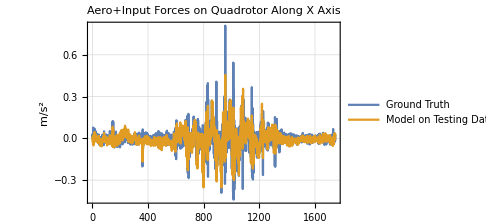
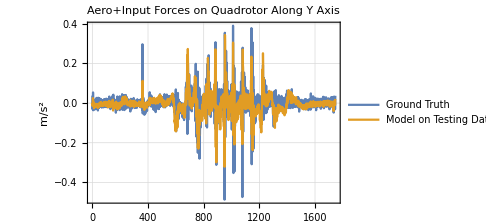
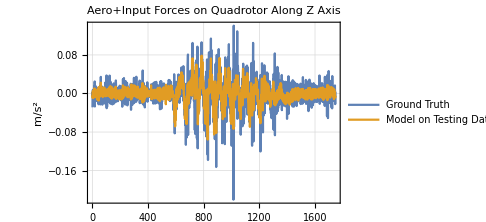
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{groundTruthF,testingOutputF,groundTruthT,testingOutputT,labels},
groundTruthF=𝕐𝒻ᵀ;
testingOutputF=𝔻.ℤ𝒻ᵀ;
groundTruthT=𝕐𝓉ᵀ;
testingOutputT=𝔼.ℤ𝓉ᵀ;
labels={"X","Y","Z"};
{Table[
ListPlot[{groundTruthF⟦i⟧,testingOutputF⟦i⟧},
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Testing Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}],
Table[
ListPlot[{groundTruthT⟦i,;;;;10⟧,testingOutputT⟦i,;;;;10⟧},
PlotTheme->"Detailed",
Joined->True,
PlotLabel->"Aero+Input Forces on Quadrotor Along "<>labels⟦i⟧<>" Axis",
PlotLegends->Placed[{"Ground Truth","Model on Testing Data"},Bottom],
PlotRange->All,
ImageSize->Medium,
FrameLabel->{None,"m/s^2"}]
,{i,3}]
}
]//TableForm
```

```mathematica
Module[{𝓎f,𝓎t,𝕗,τ,N},
𝓎f=Mean[𝕐𝒻];𝓎t=Mean[𝕐𝓉];𝕗=(𝔻.ℤ𝒻ᵀ)ᵀ;τ=(𝔼.ℤ𝓉ᵀ)ᵀ;N=Length[𝕗];
{1-(∑_(i=1)^N Norm[𝕐𝒻⟦i⟧-𝕗⟦i⟧])/(∑_(i=1)^N Norm[𝕐𝒻⟦i⟧-𝓎f]),
1-(∑_(i=1)^N Norm[𝕐𝓉⟦i⟧-τ⟦i⟧])/(∑_(i=1)^N Norm[𝕐𝓉⟦i⟧-𝓎t])}//TableForm
]
```

0.961393
0.164753